# Dart throw analysis

The idea of this exercise is to see how variable our movements are in a repeated, constrained task. You will throw a dart three times. Try to be ask consistent as you can, aiming for the red dot in the center of the target (the Bullseye!).

Each throw will be recorded using a phone video camera.  We will use a machine learning tool to track your positions. For 2024, this tool is not well trained - with your permission, we will add your videos to the training data set to improve its function.

We want to examine the variability between your throws.  We can examine this variability by comparing the positions of your body in each recording, and by comparing the time-varying velocities of your elbow, wrist, and hand.

## Import data

This will open a window  to select the CSV file with the data.

```mathematica
(*Open file selector dialog*)
fileDialogResult=SystemDialogInput["FileOpen","*.csv"];
data=Import[fileDialogResult,"CSV","SkipLines"->3];
```

## Extract data and plot

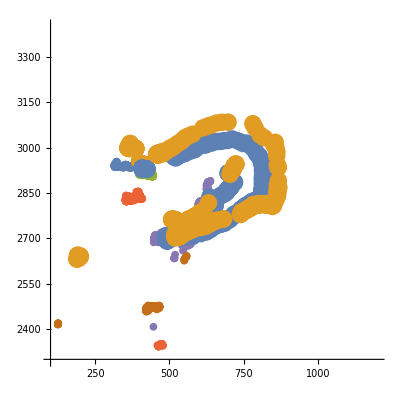

```mathematica
(*Extract x,y,z data and substract the mean for each*)
ear=data[[All,2;;3]];ear[[All,2]]=Abs[ear[[All,2]]-3600];cear=data[[All,4]];
eye=data[[All,5;;6]];eye[[All,2]]=Abs[eye[[All,2]]-3600];ceye=data[[All,7]];
mouth=data[[All,8;;9]];mouth[[All,2]]=Abs[mouth[[All,2]]-3600];cmouth=data[[All,10]];
shoulder=data[[All,11;;12]];shoulder[[All,2]]=Abs[shoulder[[All,2]]-3600];cshoulder=data[[All,13]];
elbow=data[[All,14;;15]];elbow[[All,2]]=Abs[elbow[[All,2]]-3600];celbow=data[[All,16]];
wrist=data[[All,17;;18]];wrist[[All,2]]=Abs[wrist[[All,2]]-3600];cwrist=data[[All,19]];
knuckle=data[[All,20;;21]];knuckle[[All,2]]=Abs[knuckle[[All,2]]-3600];cknuckle=data[[All,22]];
waist=data[[All,23;;24]];waist[[All,2]]=Abs[waist[[All,2]]-3600];cwaist=data[[All,25]];
toe=data[[All,26;;27]];toe[[All,2]]=Abs[toe[[All,2]]-3600];ctoe=data[[All,28]];

xAxisRange={100,1200};
yAxisRange={2300,3400};
dots=ListPlot[{ear,eye,mouth,shoulder,elbow,waist,toe},PlotMarkers->{"•", 8},AspectRatio->1,PlotRange->{xAxisRange,yAxisRange}];
hands=ListPlot[{wrist,knuckle},PlotMarkers->{"•", 18},AspectRatio->1,PlotRange->{xAxisRange,yAxisRange}];
Show[dots,hands]
```

## Calculate instantaneous velocity and plot

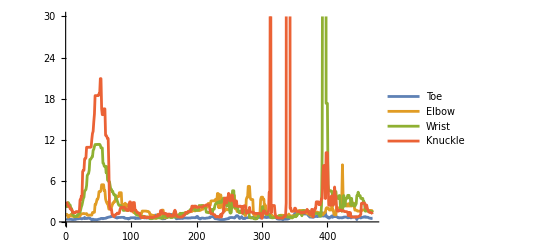

```mathematica
dEar=MedianFilter[EuclideanDistance@@@Partition[ear,2,1],5];
dEye=MedianFilter[EuclideanDistance@@@Partition[eye,2,1],5];
dMouth=MedianFilter[EuclideanDistance@@@Partition[mouth,2,1],5];
dShoulder=MedianFilter[EuclideanDistance@@@Partition[shoulder,2,1],5];
dElbow=MedianFilter[EuclideanDistance@@@Partition[elbow,2,1],5];
dWrist=MedianFilter[EuclideanDistance@@@Partition[wrist,2,1],5];
dKnuckle=MedianFilter[EuclideanDistance@@@Partition[knuckle,2,1],5];
dWaist=MedianFilter[EuclideanDistance@@@Partition[waist,2,1],5];
dToe=MedianFilter[EuclideanDistance@@@Partition[toe,2,1],5];
ListLinePlot[{dToe,dElbow,dWrist,dKnuckle},PlotRange->{Automatic,{0,30}},PlotLegends->{"Toe","Elbow","Wrist","Knuckle"}]
```

```mathematica
fps=30.;
Length[toe]/fps
```

15.6667